# Global Fitting and Analysis Notebook for NTD-DBD GR constructs bound to TSG101cc–Pyrene

## Jordan White

All experiments are at 20.baC.

Buffer: 13.2 mM HEPES, 16 mM K*Acetate, 67.2 mM NaCl, 4.2 mM MgCl2, and 0.84 mM TCEP at pH 7.56 w/KOH

## Load Data

### 20180215

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180215"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180215

```mathematica
dataApyr=Drop[Import["20180215_ADBD-35nMTSG101cc-pyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
nm297Apyr=Take[Transpose[dataApyr],1];
nm280Apyr=Take[Transpose[dataApyr],{2}];
concApyr=N[Flatten[Take[Transpose[dataApyr]*10^-9,{3}]]];
dataAvgApyr20180215=Transpose[{Flatten[concApyr],Flatten[Mean[{nm297Apyr,nm280Apyr}]]}];
```

```mathematica
dataC3pyr=Drop[Import["20180215_C3DBD-35nMTSG101cc-pyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
nm297C3pyr=Take[Transpose[dataC3pyr],1];
nm280C3pyr=Take[Transpose[dataC3pyr],{2}];
concC3pyr=N[Flatten[Take[Transpose[dataC3pyr]*10^-9,{3}]]];
dataAvgC3pyr20180215=Transpose[{Flatten[concC3pyr],Flatten[Mean[{nm297C3pyr,nm280C3pyr}]]}];
```

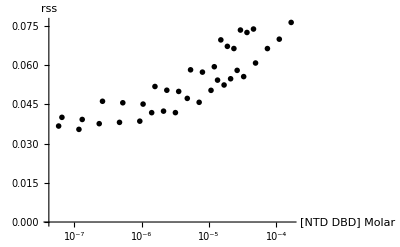

```mathematica
ListLogLinearPlot[{dataAvgApyr20180215,dataAvgC3pyr20180215},PlotRange->All,AxesLabel->{"[NTD DBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

### 20180309

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180309"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180309

```mathematica
dataApy=Drop[Import["20180309_ADBD_TSG101ccPyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
nm397Apy=Take[Transpose[dataApy],1];
nm380Apy=Take[Transpose[dataApy],{2}];
concApy=N[Flatten[Take[Transpose[dataApy]*10^-9,{3}]]];
dataAvgApyr20180309=Transpose[{Flatten[concApy],Flatten[Mean[{nm397Apy,nm380Apy}]]}];
```

```mathematica
dataC3py=Drop[Import["20180309_C3DBD_TSG101ccPyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)nm397C3py=Take[Transpose[dataC3py],1];
nm380C3py=Take[Transpose[dataC3py],{2}];
concC3py=N[Flatten[Take[Transpose[dataC3py]*10^-9,{3}]]];
dataAvgC3pyr20180309=Transpose[{Flatten[concC3py],Flatten[Mean[{nm397C3py,nm380C3py}]]}];
```

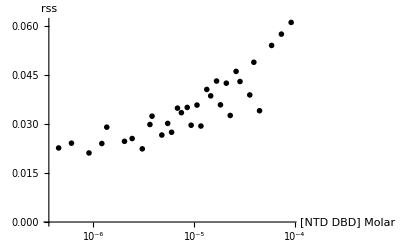

```mathematica
ListLogLinearPlot[{dataAvgApyr20180309,dataAvgC3pyr20180309},PlotRange->All,AxesLabel->{"[NTD DBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

```mathematica
dataAvgC3pyr20180309={{0.000091476,0.06107},{0.000073181,0.057495},{0.000058544,0.05403},{0.000039029800000000004,0.048885},{0.0000260198,0.046090000000000006},{0.000020816,0.042485},{0.000016653,0.043135},{0.000013322,0.040565000000000004},{0.000010658,0.035785},{8.526*^-6,0.03507},{6.821*^-6,0.034845},{5.457*^-6,0.030175},{3.638*^-6,0.029835},{2.425*^-6,0.025544999999999998},{1.213*^-6,0.024015},{6.063*^-7,0.024125},{3.032*^-7,0.03685}};
```

### 20180427

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180427"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180427

```mathematica
dataApy=Drop[Import["20180427_ADBD_TSG101ccPyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)nm397Apy=Take[Transpose[dataApy],1];
nm380Apy=Take[Transpose[dataApy],{2}];
concApy=N[Flatten[Take[Transpose[dataApy]*10^-9,{3}]]];
```

```mathematica
dataAvgApyr20180427=Transpose[{Flatten[concApy],Flatten[Mean[{nm397Apy,nm380Apy}]]}];
```

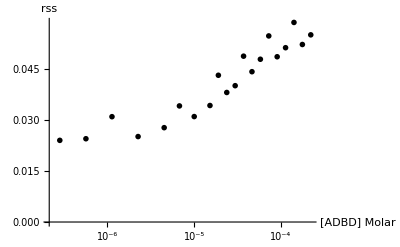

```mathematica
ListLogLinearPlot[dataAvgApyr20180427,PlotRange->All,AxesLabel->{"[ADBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

```mathematica
dataC3py=Drop[Import["20180427_C3DBD_TSG101ccPyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm397C3py=Take[Transpose[dataC3py],1];
nm380C3py=Take[Transpose[dataC3py],{2}];
concC3py=N[Flatten[Take[Transpose[dataC3py]*10^-9,{3}]]];
```

```mathematica
dataAvgC3pyr20180427=Transpose[{Flatten[concC3py],Flatten[Mean[{nm397C3py,nm380C3py}]]}];
```

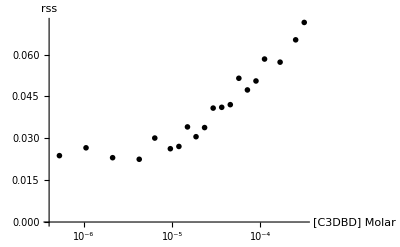

```mathematica
ListLogLinearPlot[dataAvgC3pyr20180427,PlotRange->All,AxesLabel->{"[C3DBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

### 20180504

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180504"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180504

```mathematica
dataApy=Drop[Import["20180504_ADBD_TSG101ccPyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm397Apy=Take[Transpose[dataApy],1];
nm380Apy=Take[Transpose[dataApy],{2}];
concApy=N[Flatten[Take[Transpose[dataApy]*10^-9,{3}]]];
```

```mathematica
dataAvgApyr20180504=Transpose[{Flatten[concApy],Flatten[Mean[{nm397Apy,nm380Apy}]]}];
```

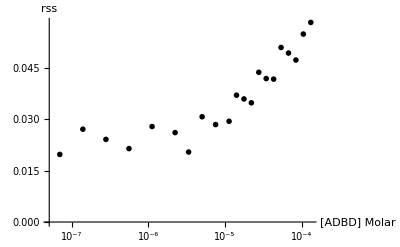

```mathematica
ListLogLinearPlot[dataAvgApyr20180504,PlotRange->All,AxesLabel->{"[ADBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

```mathematica
dataC3py=Drop[Import["20180504_C3DBD_TSG101ccPyrene.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm397C3py=Take[Transpose[dataC3py],1];
nm380C3py=Take[Transpose[dataC3py],{2}];
concC3py=N[Flatten[Take[Transpose[dataC3py]*10^-9,{3}]]];
```

```mathematica
dataAvgC3pyr20180504=Transpose[{Flatten[concC3py],Flatten[Mean[{nm397C3py,nm380C3py}]]}];
```

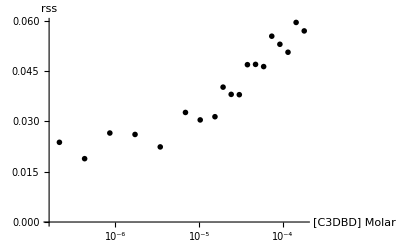

```mathematica
ListLogLinearPlot[dataAvgC3pyr20180504,PlotRange->All,AxesLabel->{"[C3DBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

## Equations

### Single Site

```mathematica
fit[bu_,bb_,mu_,x_,kd_]:=(bu+mu*Log[x])*1/(1+x/kd)+bb*(x/kd)/(1+x/kd);
```

```mathematica
model[bu0_,bb0_,mu0_,bu1_, bb1_, mu1_,bu2_,bb2_,mu2_,x_,kd_,set_]:=Which[set==0,Evaluate@fit[bu0,bb0,mu0,x,kd],
set==1,Evaluate@fit[bu1,bb1,mu1,x,kd],
set==2,Evaluate@fit[bu2,bb2,mu2,x,kd]];
```

### Two GR and Two TSG101cc

```mathematica
fit2[bu_,bb_,tsg_,x_,kd1_,kd2_]:=bu*1/(1+x/kd1+x^2*tsg/(kd1^2*kd2))+0.5bb*(x/kd1)/(1+x/kd1+x^2*tsg/(kd1^2*kd2))+bb*(x^2*tsg/(kd1^2*kd2))/(1+x/kd1+x^2*tsg/(kd1^2*kd2));
```

```mathematica
model2[bu0_,bb0_,bu1_, bb1_, bu2_,bb2_,x_,kd1_,kd2_,set_]:=Which[set==0,Evaluate@fit2[bu0,bb0,7.6*10^-8,x,kd1,kd2],
set==1,Evaluate@fit2[bu1,bb1,7.6*10^-8,x,kd1,kd2],
set==2,Evaluate@fit2[bu2,bb2,7.6*10^-8,x,kd1,kd2]];
```

### Data Setting

```mathematica
globalA=Join[dataAvgApyr20180309/.{x_,y_}->{0,x,y},
dataAvgApyr20180427/.{x_,y_}->{1,x,y},
dataAvgApyr20180504/.{x_,y_}->{2,x,y}];
globalC3=Join[dataAvgC3pyr20180309/.{x_,y_}->{0,x,y},
dataAvgC3pyr20180427/.{x_,y_}->{1,x,y},
dataAvgC3pyr20180504/.{x_,y_}->{2,x,y}];
```

The below model set up includes preliminary data from February 15th 2018. TSG101cc-pyrene was at 35 nM that day, about half the concentration of the other data here. Both datasets from that day exhibit what looks like a logarithmic unbound baseline, but it is not entirely clear.

```mathematica
(*model[bu0_,bb0_,mu0_,bu1_, bb1_, mu1_,bu2_,bb2_,mu2_,bu3_,bb3_,mu3_,x_,kd_,set_]:=Which[set==0,Evaluate@fit[bu0,bb0,mu0,x,kd],
set==1,Evaluate@fit[bu1,bb1,mu1,x,kd],
set==2,Evaluate@fit[bu2,bb2,mu2,x,kd],
set==3,Evaluate@fit[bu3,bb3,mu3,x,kd]];
globalA=Join[dataAvgApyr20180215/.{x_,y_}->{0,x,y},
dataAvgApyr20180309/.{x_,y_}->{1,x,y},
dataAvgApyr20180427/.{x_,y_}->{2,x,y},
dataAvgApyr20180504/.{x_,y_}->{3,x,y}];
globalC3=Join[dataAvgC3pyr20180215/.{x_,y_}->{0,x,y},
dataAvgC3pyr20180309/.{x_,y_}->{1,x,y},
dataAvgC3pyr20180427/.{x_,y_}->{2,x,y},
dataAvgC3pyr20180504/.{x_,y_}->{3,x,y}];*)
```

## Fit the Data

#### A DBD

```mathematica
nlmApy=NonlinearModelFit[globalA,model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,set],{{kd,3*10^-5},{bb0,0.12},{bu0,0.03},{bb1,0.12},{bu1,0.03},{bu2,0.03},{bb2,0.07}},{set,gr},MaxIterations->1000,Method->"LevenbergMarquardt"]
```

FittedModel[Which[set==0,«4»,0.0224551/(1+gr/(«23»))+(0.0629586 gr)/((1+gr/(«23»)) 0.0000335832)]]

{kd→0.0000335832,bb0→0.0524283,bu0→0.0243219,bb1→0.0612804,bu1→0.0252366,bu2→0.0224551,bb2→0.0629586}

{7.58538×10^-6,0.00491025,0.00138771,0.00259362,0.00156363,0.00128848,0.00357035}

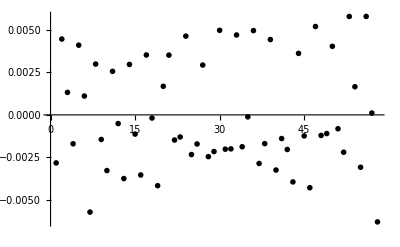

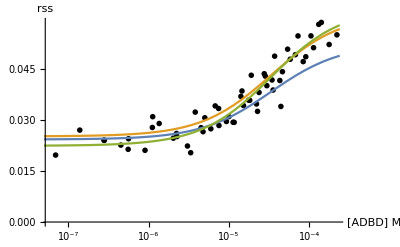

0.000593195

-0.0000152283

```mathematica
nlmApy["BestFitParameters"]
nlmApy["ParameterErrors"]
ListPlot[Reverse[nlmApy["FitResiduals"]],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{dataAvgApyr20180309,dataAvgApyr20180427,dataAvgApyr20180504},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,0]/.nlmApy["BestFitParameters"],model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,1]/.nlmApy["BestFitParameters"],model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,2]/.nlmApy["BestFitParameters"],model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,3]/.nlmApy["BestFitParameters"]},{gr,10^-9,2.4*10^-4}]]
Total[nlmApy["FitResiduals"]^2]
nlmApy["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmApy["Response"]]-Length[nlmApy["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

#### C3 DBD

```mathematica
nlmC3py=NonlinearModelFit[globalC3,model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,set],{{kd,7*10^-5},{bb0,0.12},{bu0,0.03},{bb1,0.12},{bu1,0.03},{bb2,0.12},{bu2,0.03}},{set,gr},MaxIterations->1000,Method->"LevenbergMarquardt"]
```

FittedModel[«1»]

{kd→0.0000599857,bb0→0.0835602,bu0→0.0275825,bb1→0.0750715,bu1→0.021266,bb2→0.0722293,bu2→0.0238742}

{0.0000101979,0.00559215,0.00124853,0.0032252,0.0014656,0.00367373,0.00130442}

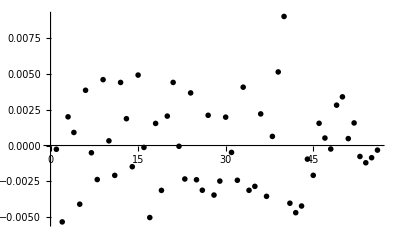

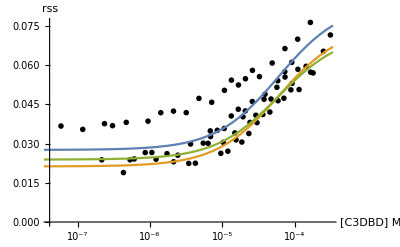

0.000520136

-0.0000204934

```mathematica
nlmC3py["BestFitParameters"]
nlmC3py["ParameterErrors"]
ListPlot[Reverse[nlmC3py["FitResiduals"]],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{dataAvgC3pyr20180309,dataAvgC3pyr20180427,dataAvgC3pyr20180504,dataAvgC3pyr20180215},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,0]/.nlmC3py["BestFitParameters"],model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,1]/.nlmC3py["BestFitParameters"],model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,2]/.nlmC3py["BestFitParameters"]},{gr,10^-8,3.4*10^-4}]]
Total[nlmC3py["FitResiduals"]^2]
nlmC3py["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmC3py["Response"]]-Length[nlmC3py["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

Below fit adds in preliminary data that used a lower TSG101cc-pyrene concentration that may have been too low. While rss is resistant to emission intensity changes, that only holds true as long as the signal is in the mid-range for the PMT. Too low or too high and noise will cause problems. Also the signal may have been bleaching. I don’t recommend using the below fit as it has obvious systematic problems in the prelim data fit.

```mathematica
globalC32=Join[dataAvgC3pyr20180309/.{x_,y_}->{0,x,y},
dataAvgC3pyr20180427/.{x_,y_}->{1,x,y},
dataAvgC3pyr20180504/.{x_,y_}->{2,x,y},
dataAvgC3pyr20180215/.{x_,y_}->{3,x,y}];
```

```mathematica
model2[bu0_,bb0_,bu1_, bb1_, bu2_,bb2_,bu3_,bb3_,x_,kd_,set_]:=Which[set==0,Evaluate@fit[bu0,bb0,0,x,kd],
set==1,Evaluate@fit[bu1,bb1,0,x,kd],
set==2,Evaluate@fit[bu2,bb2,0,x,kd],
set==3,Evaluate@fit[bu3,bb3,0,x,kd]];
```

```mathematica
nlmC3py2=NonlinearModelFit[globalC32,model2[bu0,bb0,bu1,bb1,bu2,bb2,bu3,bb3,gr,kd,set],{{kd,6*10^-5},{bb0,0.08},{bu0,0.03},{bb1,0.08},{bu1,0.03},{bb2,0.08},{bu2,0.03},{bb3,0.12},{bu3,0.04}},{set,gr},MaxIterations->1000,Method->"LevenbergMarquardt"]
```

FittedModel[Which[set==0,(«21»)/(1+«1»)+(«1»)/(«1»),«4»,set==3,0.0394781/(1+gr/(«24»))+(0.0874624 gr)/((1+gr/(«24»)) 0.000052473)]]

{kd→0.000052473,bb0→0.0803069,bu0→0.0272479,bb1→0.0730257,bu1→0.0206556,bb2→0.0700859,bu2→0.0234466,bb3→0.0874624,bu3→0.0394781}

{7.27163×10^-6,0.00440278,0.00119134,0.00259794,0.00136989,0.00292197,0.0012369,0.00345832,0.00099831}

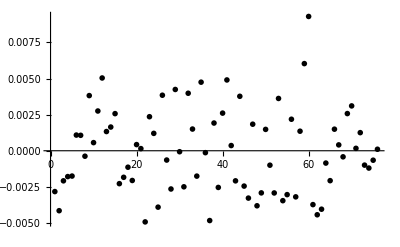

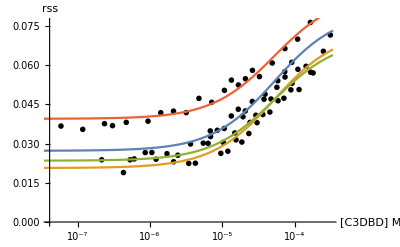

0.000638179

-0.0000145142

```mathematica
nlmC3py2["BestFitParameters"]
nlmC3py2["ParameterErrors"]
ListPlot[Reverse[nlmC3py2["FitResiduals"]],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{dataAvgC3pyr20180309,dataAvgC3pyr20180427,dataAvgC3pyr20180504,dataAvgC3pyr20180215},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{model2[bu0,bb0,bu1,bb1,bu2,bb2,bu3,bb3,gr,kd,0]/.nlmC3py2["BestFitParameters"],model2[bu0,bb0,bu1,bb1,bu2,bb2,bu3,bb3,gr,kd,1]/.nlmC3py2["BestFitParameters"],model2[bu0,bb0,bu1,bb1,bu2,bb2,bu3,bb3,gr,kd,2]/.nlmC3py2["BestFitParameters"],
model2[bu0,bb0,bu1,bb1,bu2,bb2,bu3,bb3,gr,kd,3]/.nlmC3py2["BestFitParameters"]},{gr,10^-8,3.4*10^-4}]]
Total[nlmC3py2["FitResiduals"]^2]
nlmC3py2["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmC3py2["Response"]]-Length[nlmC3py2["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

### Attempt complex formation fit:

```mathematica
nlmApy2=NonlinearModelFit[globalA,model2[bu0,bb0,bu1, bb1, bu2,bb2,gr,kd1,kd2,set],{{kd1,3*10^-5},{kd2,3*10^-5},{bb0,0.12},{bu0,0.03},{bb1,0.12},{bu1,0.03},{bu2,0.03},{bb2,0.07}},{set,gr},MaxIterations->1000,Method->"LevenbergMarquardt"]
```

FittedModel[Which[set==0,«4»,0.0224551/(1+gr/(«24»)+(«22» gr^2)/((«24»)^2 «22»))+(0.5 «20» gr)/(«24» («1»))+(«1»)/((«24»)^2 (1+«1»+(«1»)/(«1»)) «22»)]]

{kd1→0.0000335832,kd2→2.33422×10^7,bb0→0.104857,bu0→0.0243219,bb1→0.122561,bu1→0.0252366,bu2→0.0224551,bb2→0.125917}

{7.66086×10^-6,9.19587×10^-18,0.00991822,0.00140151,0.00523886,0.00157919,0.0013013,0.00721175}

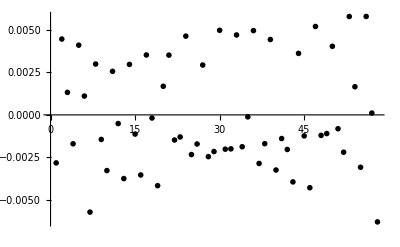

-Graphics-

0.000593195

```mathematica
nlmApy2["BestFitParameters"]
nlmApy2["ParameterErrors"]
ListPlot[Reverse[nlmApy2["FitResiduals"]],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{dataAvgApyr20180309,dataAvgApyr20180427,dataAvgApyr20180504},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{model2[bu0,bb0,bu1, bb1, bu2,bb2,gr,kd1,kd2,0]/.nlmApy2["BestFitParameters"],model2[bu0,bb0,bu1, bb1, bu2,bb2,gr,kd1,kd2,1]/.nlmApy2["BestFitParameters"],model2[bu0,bb0,bu1, bb1, bu2,bb2,gr,kd1,kd2,2]/.nlmApy2["BestFitParameters"]},{gr,10^-9,2.4*10^-4}]]
Total[nlmApy2["FitResiduals"]^2]
```

A good fit... it also is very clearly forcing a monomeric single site fit.

## Fraction Bound Outputs

### A isoform

```mathematica
nlmApy["BestFitParameters"]
```

{kd→0.0000335832,bb0→0.0524283,bu0→0.0243219,bb1→0.0612804,bu1→0.0252366,bu2→0.0224551,bb2→0.0629586}

```mathematica
Afrac0py[gr_,rss_]:=fit[0,1,0,gr,0.00003358321081747342]+(rss-(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,0]/.nlmApy["BestFitParameters"]))/(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,0]/.nlmApy["BestFitParameters"]);
Afrac1py[gr_,rss_]:=fit[0,1,0,gr,0.00003358321081747342]+(rss-(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,1]/.nlmApy["BestFitParameters"]))/(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,1]/.nlmApy["BestFitParameters"]);
Afrac2py[gr_,rss_]:=fit[0,1,0,gr,0.00003358321081747342]+(rss-(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,2]/.nlmApy["BestFitParameters"]))/(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,2]/.nlmApy["BestFitParameters"]);
```

```mathematica
fracBoundApy=Transpose[{Flatten[{Transpose[dataAvgApyr20180309][[1]],Transpose[dataAvgApyr20180427][[1]],Transpose[dataAvgApyr20180504][[1]]}],Flatten[{Afrac0py[Transpose[dataAvgApyr20180309][[1]],Transpose[dataAvgApyr20180309][[2]]],Afrac1py[Transpose[dataAvgApyr20180427][[1]],Transpose[dataAvgApyr20180427][[2]]],Afrac2py[Transpose[dataAvgApyr20180504][[1]],Transpose[dataAvgApyr20180504][[2]]]}]}];
```

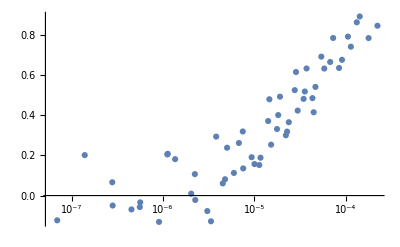

```mathematica
ListLogLinearPlot[fracBoundApy]
```

### C3 isoform

```mathematica
nlmC3py["BestFitParameters"]
```

{kd→0.0000599857,bb0→0.0835602,bu0→0.0275825,bb1→0.0750715,bu1→0.021266,bb2→0.0722293,bu2→0.0238742}

```mathematica
C3frac0py[gr_,rss_]:=fit[0,1,0,gr,0.00005998566620393823]+(rss-(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,0]/.nlmC3py["BestFitParameters"]))/(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,0]/.nlmC3py["BestFitParameters"]);
C3frac1py[gr_,rss_]:=fit[0,1,0,gr,0.00005998566620393823]+(rss-(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,1]/.nlmC3py["BestFitParameters"]))/(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,1]/.nlmC3py["BestFitParameters"]);
C3frac2py[gr_,rss_]:=fit[0,1,0,gr,0.00005998566620393823]+(rss-(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,2]/.nlmC3py["BestFitParameters"]))/(model[bu0,bb0,0,bu1,bb1,0,bu2,bb2,0,gr,kd,2]/.nlmC3py["BestFitParameters"]);
```

```mathematica
fracBoundC3py=Transpose[{Flatten[{Transpose[dataAvgC3pyr20180309][[1]],Transpose[dataAvgC3pyr20180427][[1]],Transpose[dataAvgC3pyr20180504][[1]]}],Flatten[{C3frac0py[Transpose[dataAvgC3pyr20180309][[1]],Transpose[dataAvgC3pyr20180309][[2]]],C3frac1py[Transpose[dataAvgC3pyr20180427][[1]],Transpose[dataAvgC3pyr20180427][[2]]],C3frac2py[Transpose[dataAvgC3pyr20180504][[1]],Transpose[dataAvgC3pyr20180504][[2]]]}]}];
```

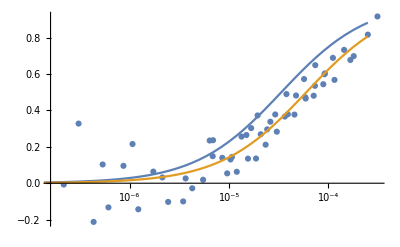

```mathematica
Show[ListLogLinearPlot[{fracBoundC3py}],
LogLinearPlot[{fit[0,1,0,gr,0.00003358321081747342],fit[0,1,0,gr,0.0000599856]},{gr,6*10^-8,2.5*10^-4}]]
```

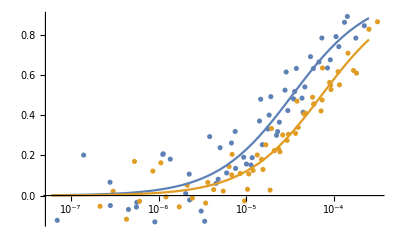

```mathematica
Show[ListLogLinearPlot[{fracBoundApy,fracBoundC3py}],
LogLinearPlot[{fit[0,1,0,gr,0.00003358321081747342],fit[0,1,0,gr,0.0000599856]},{gr,6*10^-8,2.5*10^-4}]]
```

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/"]
Export["GlobalFit-ADBD_TSG101ccPyrene.csv",N[fracBoundApy]];
Export["GlobalFit-C3DBD_TSG101ccPyrene.csv",N[fracBoundC3py]];
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy